# Quantum rotor F=1

```mathematica
ClearAll["`*"];
ClearAll["Global`*"];
```

## Parameters

```mathematica
sizex=1;(* sizex=1 *)
xr=0.5 sizex;
yr=xr;
α0=4000;
α1=8000;
E0=0.5;
I1=1.5
```

1.5

```mathematica
Fx=1/(√2){{0,1,0},{1,0,1},{0,1,0}};
Fy=1/(√2){{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Fz={{1,0,0},{0,0,0},{0,0,-1}};
Fr=1/(√2){{0,(x-ⅈ y)/Sqrt[x^2+y^2],0},{(x+ⅈ y)/Sqrt[x^2+y^2],0,(x-ⅈ y)/Sqrt[x^2+y^2]},{0,(x+ⅈ y)/Sqrt[x^2+y^2],0}};
```

```mathematica
{((Fx.Fy-Fy.Fx)-ⅈ Fz)//MatrixForm, ((Fy.Fz-Fz.Fy)-ⅈ Fx)//MatrixForm, ((Fz.Fx-Fx.Fz)-ⅈ Fy)//MatrixForm}
```

{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

## Derivation of V and B (anisotropic)

```mathematica
setangle[angle_] :=Module[{degs,q,xyrotation,rs},
degs = {0, angle, Pi, Pi+angle};
rs = {xr,yr,xr,yr};
currentAngle = angle;
beta=1/Sqrt[2];
xyrotation= RotationMatrix[angle/2, {0,0,1}];
q[deg_] := {Cos[deg], Sin[deg], 0}; 
Evec[x_, y_, z_]:=Sum[(Sqrt[1-beta^2]{0, 0, 1}+beta Cross[q[degs[[i]]], {0,0,1}])Exp[2Pi I /(2*rs[[i]])*q[degs[[i]]].xyrotation.{x,y,z}], {i,1,4}]; (*dodac /(2*rs[[i]])?*)


nxr = xr/(2Cos[angle/2]);
nyr = yr/(2Sin[angle/2]);
vscalar[x_, y_]:=(-((α0 E0^2)/4))*Conjugate[Evec[x, y, 0]] . Evec[x, y, 0];
bvector[x_, y_]:=(-((I α1 E0^2)/(4*(2*I1 + 1))))*Cross[Conjugate[Evec[x, y, 0]], Evec[x, y, 0]];
V=vscalar[x,y] (* LICZY SIĘ!*);
{Bx,By,zero}=xyrotation.bvector[x,y];]
```

```mathematica
ANGLE =90*Pi/180;
setangle[ANGLE]
```

```mathematica
ContourPlot[vscalar[x,y], {x,-xr*2,xr*2},{y,-yr*2,yr*2}]
```

-Graphics-

## Solving the equations

### Bulk states

```mathematica
Remove[fsol]
```

```mathematica
{xn,yn}={1,1};(* supercell size n x m (e.g. 2x2 )*)

fsol[B_,kx_,ky_,a_:1,b_:1,shift_, numi_ : 12]:=(*fsol[B,kx,ky,a,b,shift, numi]=*)NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y],ψ3[x,y]}),

PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nxr<=x<=(2 xn-1) nxr)&&(y==-nyr),(#+2 yn nyr {0,1})&],
PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nyr<=y<=(2 yn-1) nyr)&&(x==-nxr),(#+2 xn nxr {1,0})&]},{ψ1,ψ2, ψ3},{x,-nxr,+(2 xn-1) nxr},{y,-nyr,+(2 yn-1) nyr},
numi, (*number of states calculated*)
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

### Strip with Dirichlet boundary conditions at y = ± y_max

```mathematica
Remove[fEsol]
```

```mathematica
(*{xn}={1};*)
fEsol[B_,kx_,yn_Integer,a_:1,b_:1,shift_]:=fEsol[B,kx,yn,a,b,shift]=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nyr<=y<=(2 yn-1) nyr)&&(x==-nxr),(#+2 xn nxr {1,0})&],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(y==-nyr)&&(-nxr<x<nxr)],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(y==+(2 yn-1) nyr)&&(-nxr<x<nxr)]},
{ψ1,ψ2, ψ3},{x,-nxr,+nxr},{y,-nyr,+(2 yn-1) nyr},
9 yn,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

Boundary conditions at x = +- nxr

```mathematica
Remove[fEsol2]
```

```mathematica
(*{yn}={1};*)
fEsol2[B_,ky_,xn_Integer,a_:1,b_:1,shift_]:=fEsol2[B,ky,xn,a,b,shift]=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),

PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nxr<=x<=(2 xn-1) nxr)&&(y==-nyr),(#+2 yn nyr {1,0})&],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(x==-nxr)&&(-nyr<y<nyr)],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(x==+(2 xn-1) nxr)&&(-nyr<y<nyr)]},
{ψ1,ψ2, ψ3},{y,-nyr,+nyr},{x,-nxr,+(2 xn-1) nxr},
9 xn,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

### Rectangle with Dirichlet bound conditions at x = ± x_max and y = ± y_max

```mathematica
Remove[fEEsol]
fEEsol[B_,{xn_Integer,yn_Integer},a_:1,b_:1,shift_]:=(*fEEsol[B,{xn,yn},a,b,shift]=*) NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y],{x,y}],
-1/2 Laplacian[ψ2[x,y],{x,y}],
-1/2 Laplacian[ψ3[x,y],{x,y}]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x, y] == 0},True]},
{ψ1,ψ2, ψ3},{x,-nxr,+(2 xn-1) nxr},{y,-nyr,+(2 yn-1) nyr},
3*xn*yn,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

```mathematica
nxr
nyr
```

0.353553

0.353553

```mathematica
GuessShift[B_,a_] := -1.1B- 3200*a^2-200
```

```mathematica
Remove[estimateY]
Remove[PlotEnergyFromParameter]
estimateY[y1_,y2_,dx1_,dx2_]:=y2+(y2-y1)/(dx1)*dx2
PlotEnergyFromParameter[d_,join_ : True] := Module[{data, dx1, dx2, i, x, ys,plotted,sortedIndices},
data = d;
Do[
dx1 = data[[i-1,1]]-data[[i-2,1]];
dx2 =data[[i,1]]-data[[i-1,1]];
sortedIndices=Ordering[estimateY[data[[i-2, 2]],data[[i-1,2]],dx1,dx2]];
data[[i,2]][[sortedIndices]]= data[[i,2]],
{i,4,Length[data]}];
x = First[Transpose[data]];
ys = Transpose[Last[Transpose[data]]];
plotted=ListPlot[Table[Transpose[{x, ys[[i]]}],{i, Length[ys]}], Joined->join, InterpolationOrder->1, PlotRange->All];
Return[plotted]]
```

```mathematica
Remove[crossingB]
crossingB[d_] := Module[{data, dx1, dx2, i, xs, ys, f1, f2, r,intersections, sortedIndices},
data = d;
Do[
dx1 = data[[i-1,1]]-data[[i-2,1]];
dx2 =data[[i,1]]-data[[i-1,1]];
sortedIndices=Ordering[estimateY[data[[i-2, 2]],data[[i-1,2]],dx1,dx2]];
data[[i,2]][[sortedIndices]]= data[[i,2]],
{i,4,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[Last[Transpose[data]]];
f1=Interpolation[Transpose[{xs,ys[[1]]}],InterpolationOrder->3];
f2=Interpolation[Transpose[{xs,ys[[2]]}],InterpolationOrder->3];
(*intersections=x/. NSolve[f1[x]==f2[x],{x,First[xs], Last[xs]}];
r = Min[intersections]; But assuming only one root we can simply write:*)
r = x /.FindRoot[f1[x]-f2[x],{x,First[xs],Last[xs]}];
(*Show[ListPlot[Table[Transpose[{xs, ys[[i]]}],{i, Length[ys]}], Joined->False, InterpolationOrder->1, PlotRange->All]];*)
Return[r]]
```

```mathematica
Remove[EnergyDelta]
EnergyDelta[B_,a_:0.3,b_:2,shift_:-1500] := Module[{d}, d=Chop[First[fsol[B,0,0,a,b,shift, 2]]]; Return[Abs[d[[1]] - d[[2]]]]]
```

```mathematica
Remove[EnDeMin]
EnDeMin[B_,a_:0.3,b_:2,shift_:-1500] := Module[{d}, d=Sort[Chop[First[fsol[B,0,0,a,b,shift, 2]]]]; Return[{Abs[d[[2]] - d[[1]]],d[[1]]}]]
```

```mathematica
linecross[x1_,x2_,y11_,y12_,y21_,y22_] := Module[{m1,m2,b1,b2},
m1=(y22-y11)/(x2-x1);
m2=(y21-y12)/(x2-x1);
b1=y11-m1 x1;
b2=y12-m2 x1;
Return[(b2-b1)/(m1-m2)];]
```

```mathematica
Remove[BracketLowerer]
```

```mathematica
BracketLowerer[a_,b_,shift_,inx1_, inx2_,inx4_, iny1_, iny2_,iny4_, precision_] := Module[{x1,x2,x3,x4,y1,y2,y3,y4, l, ratio,e1, e4,sh,sh1,sh2,sh3,sh4,reqDiff,currDiff,i,maxiter},
x1 = inx1;
x4 = inx4;
x2 = inx2;
y1 = iny1;
y4 = iny4;
y2 = iny2;
ratio = 3/2 - Sqrt[5]/2;
l = x4-x1;
x3 = x4 - l*ratio;
{y3,sh3} = EnDeMin[x3, a, b, shift];

(*passing the information of the lowest point (in terms of Energy, not En Delta*)
sh=shift;
sh1=shift;
sh4 = shift;
sh2= shift;

reqDiff=5;
currDiff=reqDiff*2;
i=0;
maxiter=15;
While[And[Or[x4-x1>precision,currDiff>reqDiff],i<maxiter],
(*Print[{x1,x2,x3,x4}];*)
If[y2>y3,
x1=x2;
x2=x3;
x3 = x4 - (x2-x1);

y1=y2;
y2 = y3;

sh1=sh2;
sh2=sh3;

{y3,sh3} = EnDeMin[x3, a, b, sh];,
currDiff=y3;
(*else*)

x4=x3;
x3=x2;
x2 = x1 + (x4-x3);

y4=y3;
y3 = y2;

sh4 = sh3;
sh3=sh2;

{y2,sh2} = EnDeMin[x2, a, b, sh];
currDiff=y2;
];
sh = Min[sh1,sh2,sh3,sh4]*1.02;
i = i+1;
];
(*Return [(x2+x3)/2]*)
(*albo lepiej - można obliczyć punkty (energie) w x1 i x4 i poprowadzić dwie proste
To pozwala na dokładniejszy wynik przy gorszej precyzji -> szybciej*)
If[y2>y3,
x1=x2;,
(*else*)
x4=x3;
];
If[i==maxiter,Return[-currDiff];];
e1 = Chop[First[Transpose[Sort[Transpose[fsol[x1,0,0,a,b,-shift, 2]]]]]];
e4= Chop[First[Transpose[Sort[Transpose[fsol[x4,0,0,a,b,-shift, 2]]]]]];
Return[linecross[x1,x4,e1[[1]],e1[[2]],e4[[1]],e4[[2]]]]

]
```

```mathematica
Remove[FindBCrossing]
FindBCrossing[a_:0.3,b_:2] := Module[{y1, y2, y4,x1, x2,x4,result, step, precision,sh},
x1 = 0;
y1 = EnergyDelta[x1, a, b, GuessShift[0,a]];
step = 1;
x2 = step;
y2 = EnergyDelta[x2, a, b, GuessShift[x2,a]];
step = step*GoldenRatio;
x4 = x2+step;
{y4,sh} = EnDeMin[x4, a, b, GuessShift[x4,a]];
While [y2 > y4,
x1 = x2;
y1 = y2;
x2 = x4;
y2 = y4;
step = step*GoldenRatio;
x4=x4+step;
{y4,sh} = EnDeMin[x4, a, b, GuessShift[x4, a]];];
precision=(x1+x4)/2*0.15;
(*after this we know the anwser is between left and right*)
result = BracketLowerer[a,b,sh, x1,x2,x4,y1,y2,y4, precision];
Return[Re[result]]]
```

```mathematica
PlotFromky[ky_,Bmax_,a_,b_,numi_]:=Module[{data,plotted},
data =Table[{B, Chop[First[Transpose[Sort[Transpose[fsol[B,0,-Abs[ky],a,b,GuessShift[B,a],numi]]]]]]},{B,0,Bmax, Bmax/10} ];
plotted = PlotEnergyFromParameter[data];
Return[plotted]]
```

```mathematica
PlotFromRotation[B_,ky_,a_,b_,numi_,minang_,maxang_,numang_]:=Module[{ang,angtab,data,row,plotted},
data={};
angtab = Reverse[ Table[ang*Pi/180, {ang, minang, maxang, (maxang-minang)/numang}]];
Do[
ProgressIndicator[i/Length[angtab]];
ang =angtab[[i]];
setangle[ang];
row ={ang*180/Pi, Chop[First[Transpose[Sort[Transpose[fsol[B,0,-Abs[ky],a,b,GuessShift[B,a],numi]]]]]]};
AppendTo[data,row];
(*Print[{{currentAngle,row[[2]]}}];*)
,{i,1,Length[angtab]}];
plotted = PlotEnergyFromParameter[data,False];
Return[plotted]]
```

```mathematica
(*Plot from rotation (B, ky, a, b, liczba stanow, min ,i max kąt, liczba punktów w x -> łącznie numi*numang*)
```

```mathematica
FindCrossfromAngle[ANG_,a_] := Module[{},
setangle[ANG*Pi/180];
Return[FindBCrossing[a,2]]]
```

```mathematica
AnFsol[ANG_, B_,kx_,ky_,a_:1,b_:1,shift_, numi_ : 12]:=Module[{},
setangle[ANG*Pi/180];
fsol[B,kx,ky,a,b,shift, numi]]
```

```mathematica
corFun[G1_,G2_] := Abs[Correlation[Flatten[G1],Flatten[G2]]]
```

```mathematica
(*Input is a series of matrices and output the ordering (sortedIndices) which maximizes correlation between corresponding matrices
Warning: this is O(m!)*)
Remove[IdxFromGrids]
IdxFromGrids[oldGrids_, newGrids_] := Module[{m ,N, corrMatrix,zerMatrix, asign},
m = Length[oldGrids];
N = Length[oldGrids[[1]]];
corrMatrix = Table[corFun[G1,G2],{G1, oldGrids},{G2,newGrids}];
zerMatrix = Join[Transpose[Join[Table[0,{m},{m}],Transpose[corrMatrix]]],Table[0,{m},{2 m}]];
asign = Cases[FindIndependentEdgeSet[WeightedAdjacencyGraph[zerMatrix]],DirectedEdge[i_,j_]:>{i,j-m}];
Return[Transpose[asign][[2]]];]
```

```mathematica
Remove[PlotEnergyFromWAVE]
(*Takes in { {Bvalue, {{Energies},{{f1x, f1y, f1z},...}} , ...}
so d[[ B number, 1 or 2: B or other, 1 or 2: Energies or WaveF, Lvl num,  1-2-3 : x-y-z]]*)
PlotEnergyFromWAVE[d_,join_ : True, Ngrid_ : 10, intpol_ :  1] := Module[{data, oldGrids,newGrids, i, xs,ys,plotted,sortedIndices},
data = d;
oldGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[1,2,2]]}];
Do[
newGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[i,2,2]]}];

sortedIndices=IdxFromGrids[oldGrids,newGrids];
data[[i,2,1]]= data[[i,2,1]][[sortedIndices]];
data[[i,2,2]]= data[[i,2,2]][[sortedIndices]];
oldGrids = newGrids[[sortedIndices]],
{i,2,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[First[Transpose[Last[Transpose[data]]]]];
plotted=ListPlot[Table[Transpose[{xs, ys[[i]]}],{i, Length[ys]}], Joined->join, InterpolationOrder->1, PlotRange->All];
Return[plotted]]
```

```mathematica
currentAngle
```

π/2

```mathematica
{xn, yn}
```

{1,1}

```mathematica
(*
   0       1
 1x1,    2x2
 Dir,    Per
a=0.3, a=0.15

...k{alpha}
*)
```

```mathematica
{xn, yn} = {1,1}
```

{1,1}

```mathematica
d000k90 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],3]]],3]]]},{B,0.1,50, 3} ];
```

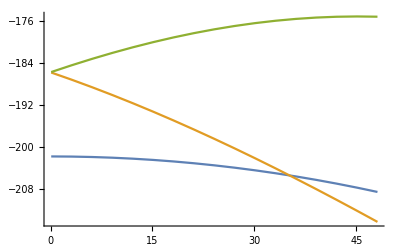

```mathematica
PlotEnergyFromWAVE[d000k90, True,10, 3]
```

```mathematica
d001k90 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.15,2,GuessShift[B,0.15],3]]],3]]]},{B,0.1,8, 0.5} ];
```

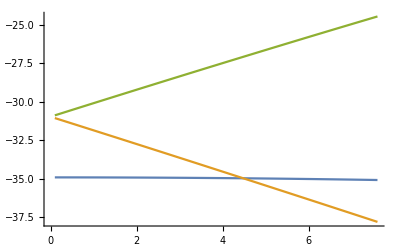

```mathematica
PlotEnergyFromWAVE[d001k90, True,10, 3]
```

```mathematica
d010k90 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{1,1},0.3,2,GuessShift[B,0.3]]]],3]]]},{B,0.01,50,3} ];
```

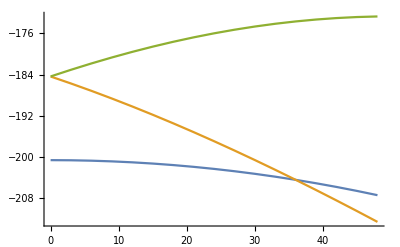

```mathematica
PlotEnergyFromWAVE[d010k90, True,10, 3]
```

```mathematica
d011k90 =  Table[{B, Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{1,1},0.15,2,GuessShift[B,0.15]]]],3]]]},{B,0.1,8,0.5} ];
```

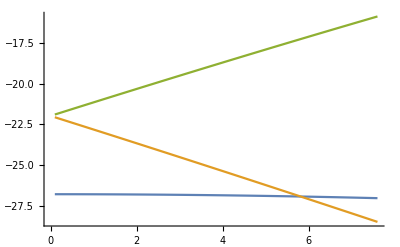

```mathematica
PlotEnergyFromWAVE[d011k90, True,10, 3]
```

```mathematica
{xn,yn} = {2,2};
```

```mathematica
{xn,yn}
```

{2,2}

```mathematica
d100k90 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],12]]],12]]]},{B,0.1,50, 3} ];
```

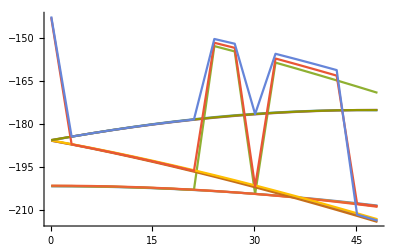

```mathematica
PlotEnergyFromWAVE[d100k90, True,10, 3]
```

```mathematica
d101k90 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.15,2,GuessShift[B,0.15],12]]],12]]]},{B,0.1,8, 0.5} ];
```

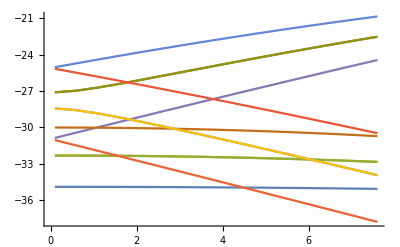

```mathematica
PlotEnergyFromWAVE[d101k90, True,10, 3]
```

```mathematica
d110k90 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{2,2},0.3,2,GuessShift[B,0.3]]]],12]]]},{B,0.01,50,3} ];
```

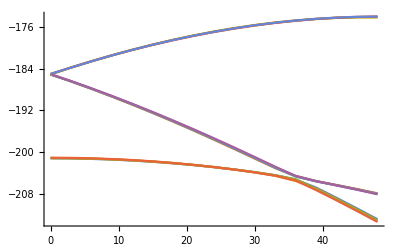

```mathematica
PlotEnergyFromWAVE[d110k90, True,10, 3]
```

```mathematica
d111k90 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{2,2},0.15,2,GuessShift[B,0.15]]]],12]]]},{B,0.01,8,0.5} ];
```

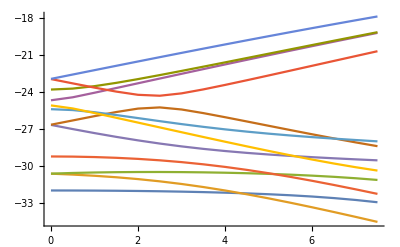

```mathematica
PlotEnergyFromWAVE[d111k90, True,10, 3]
```

```mathematica
setangle[75*Pi/180]
```

```mathematica
currentAngle/Pi*180
```

75

```mathematica
{xn,yn}
```

{1,1}

```mathematica
{xn,yn} = {1,1}
```

{1,1}

```mathematica
FindBCrossing[0.3]
```

31.4311

```mathematica
FindBCrossing[0.15]
```

4.42164

```mathematica
d000k75 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],3]]],3]]]},{B,0.1,50, 3} ];
```

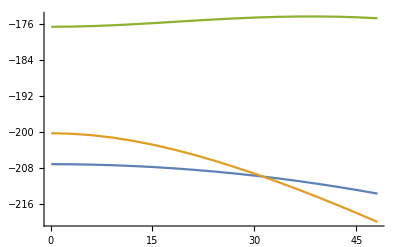

```mathematica
PlotEnergyFromWAVE[d000k75, True,10, 3]
```

```mathematica
d001k75 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.15,2,GuessShift[B,0.15],3]]],3]]]},{B,0.1,8, 0.5} ];
```

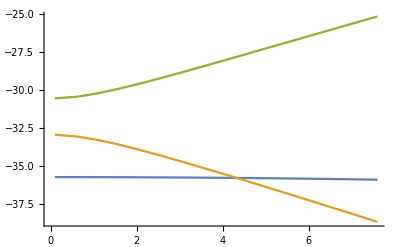

```mathematica
PlotEnergyFromWAVE[d001k75, True,10, 3]
```

```mathematica
d010k75 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{1,1},0.3,2,GuessShift[B,0.3]]]],3]]]},{B,0.01,50,3} ];
```

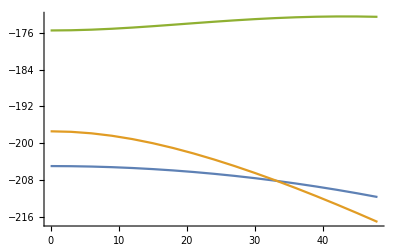

```mathematica
PlotEnergyFromWAVE[d010k75, True,10, 3]
```

```mathematica
d011k75 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{1,1},0.15,2,GuessShift[B,0.15]]]],3]]]},{B,0.01,8,0.5} ];
```

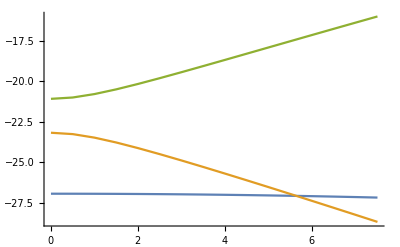

```mathematica
PlotEnergyFromWAVE[d011k75, True,10, 3]
```

```mathematica
{xn,yn} = {2,2};
```

```mathematica
{xn,yn}
```

{2,2}

```mathematica
d100k75 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],12]]],12]]]},{B,0.1,50, 3} ];
```

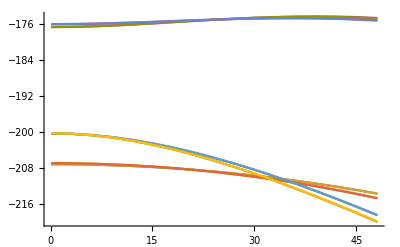

```mathematica
PlotEnergyFromWAVE[d100k75, True,10, 3]
```

```mathematica
d101k75 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.15,2,GuessShift[B,0.15],12]]],12]]]},{B,0.1,8, 0.5} ];
```

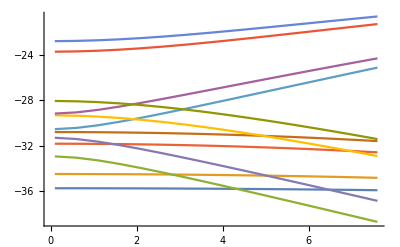

```mathematica
PlotEnergyFromWAVE[d101k75, True,10, 3]
```

```mathematica
(*Jak da się mniejsze N (obec. 10) (samplowanie jest N na N) to się nie psuje. A jak się da większe to się psuje bardziej. Do sprawdzenia*)
```

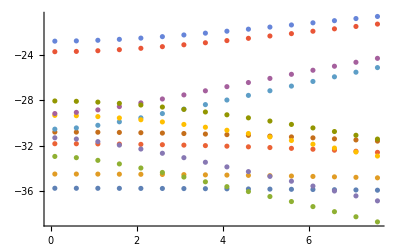

```mathematica
PlotEnergyFromWAVE[d101k75, False,10, 3]
```

```mathematica
d110k75 = Table[{B, Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{2,2},0.3,2,GuessShift[B,0.3]]]],12]]]},{B,0.01,50,3} ];
```

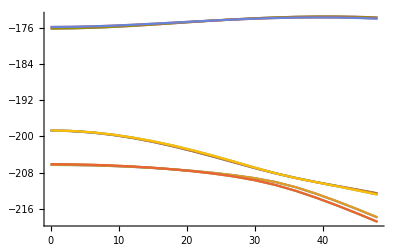

```mathematica
PlotEnergyFromWAVE[d110k75, True,10, 3]
```

```mathematica
d111k75= Table[{B,Chop[Transpose[Take[Sort[Transpose[fEEsol[B,{2,2},0.15,2,GuessShift[B,0.15]]]],12]]]},{B,0.01,8,0.5} ];
```

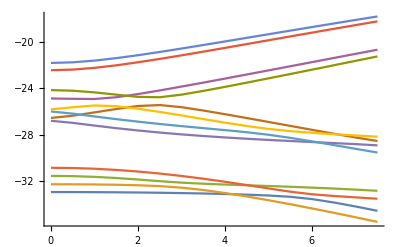

```mathematica
PlotEnergyFromWAVE[d111k75, True,10, 3]
```

```mathematica
currentAngle
```

(5 π)/12

```mathematica
ContourPlot[vscalar[x,y], {x,-xr*2,xr*2},{y,-yr*2,yr*2}]
```

-Graphics-

```mathematica
{nxr, nyr}
```

{0.315118,0.41067}

```mathematica
PrintDataWAVE[d_,Ngrid_ : 10] := Module[{data, oldGrids,newGrids, i, xs,ys,plotted,sortedIndices},
data = d;
(*takes current nxr, nyr :/ *)
oldGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[1,2,2]]}];
Do[
newGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[i,2,2]]}];

sortedIndices=IdxFromGrids[oldGrids,newGrids];
data[[i,2,1]]= data[[i,2,1]][[sortedIndices]];
data[[i,2,2]]= data[[i,2,2]][[sortedIndices]];
oldGrids = newGrids[[sortedIndices]],
{i,2,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[First[Transpose[Last[Transpose[data]]]]];
Return[{xs,ys}]]
```

```mathematica
setangle[90*Pi/180]
```

```mathematica
(*żeby nie musieć liczyć ponownie jakby co*)
```

```mathematica
PrintDataWAVE[d000k90,10]
```

{{0.1,3.1,6.1,9.1,12.1,15.1,18.1,21.1,24.1,27.1,30.1,33.1,36.1,39.1,42.1,45.1,48.1},{{-201.732,-201.76,-201.84,-201.973,-202.158,-202.395,-202.685,-203.027,-203.421,-203.868,-204.368,-204.921,-205.526,-206.184,-206.894,-207.657,-208.472},{-185.806,-187.165,-188.59,-190.079,-191.63,-193.239,-194.905,-196.624,-198.395,-200.215,-202.082,-203.994,-205.948,-207.944,-209.978,-212.049,-214.156},{-185.718,-184.433,-183.221,-182.083,-181.023,-180.042,-179.145,-178.332,-177.608,-176.973,-176.431,-175.982,-175.63,-175.376,-175.221,-175.167,-175.214}}}

```mathematica
PrintDataWAVE[d001k90,10]
```

{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},{{-34.9039,-34.9049,-34.9074,-34.9113,-34.9167,-34.9236,-34.932,-34.9418,-34.9531,-34.9659,-34.9803,-34.9961,-35.0135,-35.0324,-35.0528,-35.0748},{-31.0485,-31.4906,-31.9341,-32.3788,-32.8247,-33.2717,-33.7198,-34.169,-34.6193,-35.0706,-35.5228,-35.976,-36.4301,-36.8851,-37.341,-37.7977},{-30.872,-30.4317,-29.9928,-29.5553,-29.1193,-28.6849,-28.2522,-27.8211,-27.3918,-26.9643,-26.5388,-26.1153,-25.6938,-25.2746,-24.8577,-24.4432}}}

```mathematica
PrintDataWAVE[d010k90,10]
```

{{0.01,3.01,6.01,9.01,12.01,15.01,18.01,21.01,24.01,27.01,30.01,33.01,36.01,39.01,42.01,45.01,48.01},{{-200.633,-200.66,-200.739,-200.872,-201.058,-201.297,-201.589,-201.935,-202.333,-202.785,-203.29,-203.849,-204.46,-205.125,-205.843,-206.614,-207.438},{-184.385,-185.749,-187.177,-188.665,-190.213,-191.818,-193.477,-195.189,-196.951,-198.762,-200.619,-202.52,-204.464,-206.449,-208.472,-210.532,-212.628},{-184.376,-183.079,-181.848,-180.688,-179.6,-178.585,-177.646,-176.785,-176.002,-175.3,-174.679,-174.142,-173.688,-173.319,-173.035,-172.836,-172.723}}}

```mathematica
PrintDataWAVE[d011k90,10]
```

{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},{{-26.7977,-26.7992,-26.8027,-26.8084,-26.8161,-26.8259,-26.8378,-26.8518,-26.8679,-26.8862,-26.9065,-26.9291,-26.9538,-26.9806,-27.0097,-27.041},{-22.058,-22.4772,-22.8981,-23.3207,-23.7448,-24.1704,-24.5975,-25.0261,-25.456,-25.8874,-26.3201,-26.7541,-27.1893,-27.6258,-28.0635,-28.5023},{-21.8908,-21.4739,-21.0589,-20.6457,-20.2343,-19.825,-19.4176,-19.0122,-18.609,-18.208,-17.8092,-17.4127,-17.0186,-16.627,-16.2378,-15.8513}}}

```mathematica
PrintDataWAVE[d100k90,10]
```

{{0.1,3.1,6.1,9.1,12.1,15.1,18.1,21.1,24.1,27.1,30.1,33.1,36.1,39.1,42.1,45.1,48.1},{{-201.732,-201.76,-201.84,-201.973,-202.158,-202.395,-202.685,-203.027,-203.421,-203.868,-204.368,-204.921,-205.526,-206.184,-206.894,-207.657,-208.472},{-201.625,-201.654,-201.738,-201.877,-202.071,-202.319,-202.623,-202.981,-203.395,-203.863,-204.387,-204.966,-205.6,-206.289,-207.033,-207.833,-208.687},{-201.625,-201.654,-201.738,-201.877,-202.071,-202.319,-202.623,-202.981,-152.824,-154.689,-204.387,-158.591,-160.616,-162.683,-164.791,-166.935,-169.114},{-201.519,-201.55,-201.637,-201.782,-201.984,-202.244,-202.56,-202.934,-203.366,-203.855,-204.401,-205.004,-205.665,-206.384,-207.159,-207.992,-208.881},{-185.825,-187.094,-188.489,-189.948,-191.469,-193.05,-194.686,-196.378,-198.121,-199.914,-201.756,-203.642,-205.573,-207.545,-209.557,-211.607,-213.694},{-185.806,-187.165,-188.59,-190.079,-191.63,-193.239,-194.905,-196.624,-198.395,-200.215,-202.082,-203.994,-205.948,-207.944,-209.978,-212.049,-214.156},{-185.718,-184.433,-183.221,-182.083,-181.023,-180.042,-179.145,-178.332,-177.608,-176.973,-176.431,-175.982,-175.63,-175.376,-175.221,-175.167,-175.214},{-185.714,-187.018,-188.386,-189.818,-191.311,-192.863,-194.472,-196.135,-197.851,-199.618,-201.433,-203.294,-205.2,-207.149,-209.138,-211.167,-213.232},{-185.63,-184.398,-183.236,-182.145,-181.127,-180.184,-179.317,-178.528,-177.817,-177.187,-176.639,-176.172,-175.788,-175.488,-175.271,-175.139,-175.091},{-185.608,-184.412,-183.227,-182.114,-181.075,-180.114,-179.233,-178.432,-177.715,-177.083,-176.536,-176.078,-175.709,-175.43,-175.241,-175.145,-175.141},{-142.822,-187.094,-188.489,-189.948,-191.469,-193.05,-194.686,-196.378,-151.668,-153.439,-201.756,-157.166,-159.109,-161.098,-163.13,-207.833,-208.687},{-142.488,-184.412,-183.227,-182.114,-181.075,-180.114,-179.233,-178.432,-150.346,-152.001,-176.536,-155.515,-157.359,-159.256,-161.2,-211.607,-213.694}}}

```mathematica
PrintDataWAVE[d101k90,10]
```

{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},{{-34.9039,-34.9049,-34.9074,-34.9113,-34.9167,-34.9236,-34.932,-34.9418,-34.9531,-34.9659,-34.9803,-34.9961,-35.0135,-35.0324,-35.0528,-35.0748},{-32.3225,-32.3256,-32.333,-32.3448,-32.3611,-32.3818,-32.407,-32.4367,-32.4711,-32.5102,-32.5541,-32.6028,-32.6565,-32.7154,-32.7794,-32.8488},{-32.3225,-32.3256,-32.333,-32.3448,-32.3611,-32.3818,-32.407,-32.4367,-32.4711,-32.5102,-32.5541,-32.6028,-32.6565,-32.7154,-32.7794,-32.8488},{-31.0485,-31.4906,-31.9341,-32.3788,-32.8247,-33.2717,-33.7198,-34.169,-34.6193,-35.0706,-35.5228,-35.976,-36.4301,-36.8851,-37.341,-37.7977},{-30.872,-30.4317,-29.9928,-29.5553,-29.1193,-28.6849,-28.2522,-27.8211,-27.3918,-26.9643,-26.5388,-26.1153,-25.6938,-25.2746,-24.8577,-24.4432},{-30.0118,-30.016,-30.0264,-30.0429,-30.0656,-30.0943,-30.1293,-30.1704,-30.2177,-30.2713,-30.3311,-30.3972,-30.4696,-30.5485,-30.6337,-30.7253},{-28.4397,-28.5796,-28.848,-29.1756,-29.5317,-29.9038,-30.2862,-30.6761,-31.0716,-31.4719,-31.8763,-32.2842,-32.6953,-33.1094,-33.5262,-33.9456},{-28.4397,-28.5796,-28.848,-29.1756,-29.5317,-29.9038,-30.2862,-30.6761,-31.0716,-31.4719,-31.8763,-32.2842,-32.6953,-33.1094,-33.5262,-33.9456},{-27.1073,-26.9728,-26.7175,-26.4109,-26.0835,-25.748,-25.41,-25.0727,-24.7376,-24.406,-24.0786,-23.756,-23.4386,-23.1269,-22.8211,-22.5217},{-27.1073,-26.9728,-26.7175,-26.4109,-26.0835,-25.748,-25.41,-25.0727,-24.7376,-24.406,-24.0786,-23.756,-23.4386,-23.1269,-22.8211,-22.5217},{-25.1654,-25.4908,-25.8208,-26.1554,-26.4944,-26.8377,-27.1853,-27.5369,-27.8924,-28.2518,-28.6149,-28.9816,-29.3518,-29.7254,-30.1023,-30.4824},{-25.0366,-24.7181,-24.4046,-24.0962,-23.7931,-23.4954,-23.2033,-22.9169,-22.6363,-22.3618,-22.0934,-21.8314,-21.5759,-21.327,-21.0849,-20.8499}}}

```mathematica
PrintDataWAVE[d111k90,10]
```

{{0.01,0.51,1.01,1.51,2.01,2.51,3.01,3.51,4.01,4.51,5.01,5.51,6.01,6.51,7.01,7.51},{{-31.9784,-31.9809,-31.9884,-32.0009,-32.0188,-32.0427,-32.073,-32.1108,-32.1571,-32.2137,-32.2827,-32.3668,-32.4695,-32.5951,-32.7479,-32.9324},{-30.6173,-30.6914,-30.787,-30.9077,-31.0571,-31.238,-31.4522,-31.6998,-31.979,-32.2865,-32.6186,-32.9713,-33.341,-33.7247,-34.1197,-34.5241},{-30.6148,-30.5599,-30.5208,-30.4956,-30.4828,-30.4812,-30.4903,-30.5098,-30.5397,-30.5804,-30.6327,-30.6977,-30.7771,-30.873,-30.9881,-31.1255},{-29.2232,-29.2354,-29.2713,-29.332,-29.4192,-29.5349,-29.681,-29.859,-30.069,-30.3102,-30.5803,-30.8764,-31.195,-31.5328,-31.8867,-32.254},{-26.6654,-27.004,-27.329,-27.6356,-27.9195,-28.1773,-28.407,-28.6082,-28.7826,-28.9332,-29.0637,-29.1781,-29.2798,-29.3718,-29.4568,-29.5366},{-26.6516,-26.3044,-25.9564,-25.6223,-25.3445,-25.2489,-25.4167,-25.7103,-26.0427,-26.3881,-26.7368,-27.0841,-27.4264,-27.7604,-28.0827,-28.3898},{-25.3937,-25.4639,-25.6384,-25.8663,-26.1138,-26.3623,-26.601,-26.8237,-27.0274,-27.2109,-27.3754,-27.5229,-27.6562,-27.7781,-27.8914,-27.9983},{-25.0871,-25.3322,-25.7033,-26.0894,-26.4793,-26.8697,-27.259,-27.6456,-28.0281,-28.4047,-28.7729,-29.13,-29.4723,-29.7954,-30.0949,-30.3664},{-24.6722,-24.428,-24.0596,-23.6776,-23.2931,-22.909,-22.5262,-22.1455,-21.7672,-21.3916,-21.019,-20.6498,-20.2841,-19.9223,-19.5645,-19.2111},{-23.8018,-23.7239,-23.5265,-23.2595,-22.9549,-22.6296,-22.2923,-21.9479,-21.5994,-21.2486,-20.8971,-20.5457,-20.1952,-19.8463,-19.4995,-19.1552},{-22.9517,-23.3021,-23.6447,-23.9671,-24.228,-24.3027,-24.1105,-23.7896,-23.4265,-23.0471,-22.66,-22.269,-21.8761,-21.4825,-21.089,-20.6962},{-22.9376,-22.5843,-22.2306,-21.8777,-21.5265,-21.1775,-20.8312,-20.4879,-20.1478,-19.8114,-19.4787,-19.15,-18.8256,-18.5056,-18.1903,-17.8799}}}

```mathematica
setangle[75*Pi/180]
```

```mathematica
PrintDataWAVE[d000k75,10]
```

{{0.1,3.1,6.1,9.1,12.1,15.1,18.1,21.1,24.1,27.1,30.1,33.1,36.1,39.1,42.1,45.1,48.1},{{-207.21,-207.237,-207.315,-207.444,-207.624,-207.854,-208.136,-208.469,-208.853,-209.287,-209.773,-210.31,-210.899,-211.538,-212.228,-212.969,-213.762},{-200.329,-200.444,-200.769,-201.297,-202.013,-202.901,-203.945,-205.128,-206.435,-207.852,-209.369,-210.974,-212.659,-214.415,-216.238,-218.12,-220.056},{-176.646,-176.605,-176.493,-176.317,-176.091,-175.832,-175.556,-175.28,-175.019,-174.786,-174.594,-174.452,-174.369,-174.352,-174.407,-174.539,-174.754}}}

```mathematica
PrintDataWAVE[d001k75,10]
```

{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},{{-35.7216,-35.7226,-35.7251,-35.729,-35.7344,-35.7412,-35.7496,-35.7594,-35.7706,-35.7834,-35.7977,-35.8135,-35.8308,-35.8497,-35.8702,-35.8922},{-32.9279,-33.0376,-33.2724,-33.586,-33.946,-34.3337,-34.7389,-35.1559,-35.5812,-36.0126,-36.4487,-36.8885,-37.3314,-37.7769,-38.2246,-38.6742},{-30.5346,-30.4269,-30.197,-29.891,-29.5415,-29.1672,-28.7783,-28.3806,-27.9777,-27.5716,-27.1641,-26.756,-26.3481,-25.9411,-25.5354,-25.1314}}}

```mathematica
PrintDataWAVE[d001k75,10]
```

{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},{{-35.7216,-35.7226,-35.7251,-35.729,-35.7344,-35.7412,-35.7496,-35.7594,-35.7706,-35.7834,-35.7977,-35.8135,-35.8308,-35.8497,-35.8702,-35.8922},{-32.9279,-33.0376,-33.2724,-33.586,-33.946,-34.3337,-34.7389,-35.1559,-35.5812,-36.0126,-36.4487,-36.8885,-37.3314,-37.7769,-38.2246,-38.6742},{-30.5346,-30.4269,-30.197,-29.891,-29.5415,-29.1672,-28.7783,-28.3806,-27.9777,-27.5716,-27.1641,-26.756,-26.3481,-25.9411,-25.5354,-25.1314}}}

```mathematica
PrintDataWAVE[d010k75,10]
```

{{0.01,3.01,6.01,9.01,12.01,15.01,18.01,21.01,24.01,27.01,30.01,33.01,36.01,39.01,42.01,45.01,48.01},{{-204.981,-205.007,-205.086,-205.218,-205.402,-205.639,-205.928,-206.27,-206.665,-207.113,-207.613,-208.165,-208.77,-209.428,-210.138,-210.9,-211.715},{-197.413,-197.524,-197.85,-198.381,-199.103,-199.999,-201.049,-202.237,-203.547,-204.966,-206.482,-208.084,-209.765,-211.515,-213.33,-215.204,-217.132},{-175.461,-175.417,-175.291,-175.091,-174.833,-174.534,-174.211,-173.882,-173.561,-173.262,-172.995,-172.769,-172.593,-172.473,-172.413,-172.417,-172.49}}}

```mathematica
PrintDataWAVE[d011k75,10]
```

{{0.01,0.51,1.01,1.51,2.01,2.51,3.01,3.51,4.01,4.51,5.01,5.51,6.01,6.51,7.01,7.51},{{-26.9273,-26.9284,-26.9315,-26.9368,-26.9441,-26.9535,-26.9651,-26.9787,-26.9944,-27.0123,-27.0323,-27.0545,-27.0788,-27.1053,-27.134,-27.165},{-23.1733,-23.2577,-23.475,-23.7743,-24.1199,-24.4924,-24.8816,-25.282,-25.6902,-26.1043,-26.523,-26.9455,-27.3711,-27.7993,-28.23,-28.6627},{-21.086,-21.0035,-20.7917,-20.5016,-20.1687,-19.8126,-19.4435,-19.0669,-18.6862,-18.3034,-17.9197,-17.5362,-17.1534,-16.7718,-16.3918,-16.0137}}}

```mathematica
PrintDataWAVE[d100k75,10]
```

{{0.1,3.1,6.1,9.1,12.1,15.1,18.1,21.1,24.1,27.1,30.1,33.1,36.1,39.1,42.1,45.1,48.1},{{-207.209,-207.236,-207.314,-207.443,-207.623,-207.854,-208.135,-208.468,-208.852,-209.287,-209.773,-210.31,-210.898,-211.537,-212.227,-212.969,-213.761},{-207.191,-207.219,-207.297,-207.426,-207.607,-207.839,-208.122,-208.456,-208.841,-209.278,-209.766,-210.305,-210.896,-211.538,-212.231,-212.976,-213.772},{-206.977,-207.01,-207.103,-207.257,-207.471,-207.747,-208.083,-208.48,-208.938,-209.456,-210.036,-210.676,-211.376,-212.137,-212.958,-213.84,-214.781},{-206.96,-206.993,-207.086,-207.24,-207.456,-207.732,-208.069,-208.467,-208.926,-209.446,-210.027,-210.669,-211.371,-212.134,-212.958,-213.841,-214.784},{-200.342,-200.441,-200.725,-201.188,-201.82,-202.609,-203.545,-204.614,-205.805,-207.107,-208.509,-210.003,-211.58,-213.233,-214.956,-216.744,-218.592},{-200.328,-200.443,-200.768,-201.296,-202.012,-202.9,-203.944,-205.127,-206.434,-207.852,-209.368,-210.973,-212.658,-214.415,-216.237,-218.119,-220.056},{-200.326,-200.425,-200.708,-201.17,-201.8,-202.588,-203.522,-204.588,-205.777,-207.076,-208.475,-209.965,-211.539,-213.189,-214.91,-216.695,-218.539},{-200.312,-200.426,-200.751,-201.277,-201.991,-202.877,-203.919,-205.099,-206.403,-207.818,-209.332,-210.934,-212.615,-214.369,-216.188,-218.067,-220.001},{-176.685,-176.645,-176.531,-176.354,-176.126,-175.864,-175.584,-175.303,-175.035,-174.794,-174.591,-174.437,-174.339,-174.305,-174.34,-174.45,-174.638},{-176.645,-176.605,-176.492,-176.316,-176.09,-175.831,-175.555,-175.279,-175.018,-174.785,-174.593,-174.451,-174.368,-174.351,-174.406,-174.538,-174.752},{-176.048,-176.022,-175.95,-175.837,-175.693,-175.527,-175.351,-175.177,-175.016,-174.877,-174.77,-174.701,-174.679,-174.707,-174.792,-174.937,-175.144},{-176.006,-175.981,-175.909,-175.799,-175.657,-175.494,-175.323,-175.154,-175.,-174.869,-174.77,-174.713,-174.702,-174.745,-174.845,-175.007,-175.234}}}

```mathematica
PrintDataWAVE[d101k75,10]
```

{{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6},{{-35.7215,-35.7225,-35.725,-35.7289,-35.7343,-35.7412,-35.7495,-35.7593,-35.7706,-35.7834,-35.7976,-35.8135,-35.8308,-35.8497,-35.8701,-35.8921},{-34.4727,-34.4747,-34.4794,-34.4868,-34.4971,-34.5101,-34.5261,-34.5449,-34.5666,-34.5913,-34.6191,-34.65,-34.6841,-34.7215,-34.7623,-34.8067},{-32.9278,-33.0376,-33.2723,-33.586,-33.9459,-34.3336,-34.7389,-35.1559,-35.5811,-36.0125,-36.4486,-36.8885,-37.3314,-37.7768,-38.2245,-38.6741},{-31.8126,-31.8171,-31.828,-31.8453,-31.8691,-31.8993,-31.9361,-31.9794,-32.0294,-32.086,-32.1494,-32.2197,-32.2968,-32.381,-32.4722,-32.5706},{-31.2924,-31.4003,-31.6291,-31.9323,-32.2784,-32.6503,-33.0388,-33.4385,-33.8464,-34.2606,-34.6798,-35.1031,-35.53,-35.9599,-36.3925,-36.8274},{-30.7874,-30.7922,-30.8038,-30.8222,-30.8474,-30.8795,-30.9184,-30.9642,-31.0169,-31.0766,-31.1432,-31.2168,-31.2975,-31.3852,-31.48,-31.5819},{-30.5346,-30.4269,-30.1969,-29.8909,-29.5415,-29.1672,-28.7783,-28.3806,-27.9776,-27.5716,-27.164,-26.7559,-26.3481,-25.941,-25.5353,-25.1313},{-29.3238,-29.356,-29.4331,-29.5521,-29.7091,-29.8998,-30.1196,-30.3646,-30.6311,-30.9161,-31.2168,-31.5313,-31.8577,-32.1944,-32.5404,-32.8945},{-29.167,-29.063,-28.8438,-28.5559,-28.2308,-27.8858,-27.5301,-27.169,-26.8058,-26.4426,-26.0806,-25.721,-25.3646,-25.0119,-24.6636,-24.3201},{-28.0609,-28.0906,-28.1617,-28.2717,-28.4171,-28.594,-28.7984,-29.0266,-29.2754,-29.542,-29.824,-30.1194,-30.4265,-30.744,-31.0707,-31.4057},{-23.7376,-23.7123,-23.652,-23.5596,-23.4391,-23.2948,-23.1312,-22.9525,-22.7622,-22.5635,-22.359,-22.1509,-21.941,-21.7308,-21.5215,-21.3144},{-22.8114,-22.7888,-22.7349,-22.6523,-22.5444,-22.4153,-22.2688,-22.1086,-21.938,-21.76,-21.5768,-21.3905,-21.2028,-21.0151,-20.8287,-20.6445}}}

```mathematica
PrintDataWAVE[d110k75,10]
```

{{0.01,3.01,6.01,9.01,12.01,15.01,18.01,21.01,24.01,27.01,30.01,33.01,36.01,39.01,42.01,45.01,48.01},{{-206.299,-206.327,-206.408,-206.544,-206.734,-206.981,-207.286,-207.654,-208.09,-208.611,-209.252,-210.097,-211.252,-212.704,-214.346,-216.107,-217.951},{-206.291,-206.318,-206.399,-206.535,-206.726,-206.974,-207.279,-207.647,-208.084,-208.605,-209.246,-210.087,-211.237,-212.685,-214.324,-216.082,-217.924},{-206.161,-206.192,-206.284,-206.439,-206.657,-206.941,-207.295,-207.728,-208.252,-208.896,-209.709,-210.755,-212.062,-213.589,-215.269,-217.059,-218.932},{-206.152,-206.183,-206.276,-206.43,-206.649,-206.933,-207.288,-207.721,-208.246,-208.889,-209.7,-210.743,-212.047,-213.569,-215.247,-217.035,-218.906},{-198.699,-198.806,-199.121,-199.635,-200.331,-201.191,-202.193,-203.313,-204.52,-205.775,-207.015,-208.167,-209.19,-210.117,-210.95,-211.775,-212.623},{-198.691,-198.798,-199.113,-199.626,-200.321,-201.18,-202.181,-203.3,-204.506,-205.761,-207.002,-208.164,-209.228,-210.127,-210.95,-211.772,-212.618},{-198.679,-198.779,-199.078,-199.565,-200.229,-201.055,-202.025,-203.121,-204.322,-205.601,-206.91,-208.15,-209.183,-210.119,-211.025,-211.935,-212.872},{-198.671,-198.771,-199.069,-199.556,-200.219,-201.044,-202.013,-203.108,-204.309,-205.587,-206.896,-208.145,-209.221,-210.13,-211.027,-211.935,-212.87},{-176.086,-176.045,-175.926,-175.738,-175.496,-175.216,-174.915,-174.61,-174.316,-174.046,-173.812,-173.623,-173.488,-173.415,-173.409,-173.478,-173.631},{-176.066,-176.025,-175.906,-175.72,-175.478,-175.2,-174.901,-174.599,-174.308,-174.042,-173.813,-173.631,-173.504,-173.44,-173.446,-173.529,-173.697},{-175.756,-175.723,-175.625,-175.471,-175.272,-175.041,-174.794,-174.543,-174.303,-174.085,-173.898,-173.751,-173.652,-173.607,-173.619,-173.694,-173.835},{-175.736,-175.703,-175.606,-175.452,-175.254,-175.025,-174.78,-174.533,-174.296,-174.081,-173.9,-173.759,-173.667,-173.63,-173.653,-173.741,-173.898}}}

```mathematica
PrintDataWAVE[d111k75,10]
```

{{0.01,0.51,1.01,1.51,2.01,2.51,3.01,3.51,4.01,4.51,5.01,5.51,6.01,6.51,7.01,7.51},{{-32.944,-32.9464,-32.9535,-32.9655,-32.9824,-33.0048,-33.0333,-33.0686,-33.1125,-33.1679,-33.242,-33.3552,-33.5522,-33.8454,-34.1906,-34.5604},{-32.272,-32.2765,-32.2901,-32.3154,-32.3585,-32.4337,-32.5659,-32.7687,-33.0278,-33.3254,-33.6503,-33.9962,-34.3587,-34.7346,-35.1216,-35.5179},{-31.5492,-31.5711,-31.634,-31.7343,-31.8642,-32.0065,-32.133,-32.2266,-32.2976,-32.3604,-32.423,-32.4895,-32.5623,-32.6433,-32.7341,-32.8364},{-30.852,-30.873,-30.9342,-31.0349,-31.1738,-31.3488,-31.5572,-31.7954,-32.0589,-32.3417,-32.6343,-32.9141,-33.1348,-33.2828,-33.4023,-33.5207},{-26.7989,-26.9757,-27.2118,-27.4333,-27.6339,-27.8128,-27.9713,-28.1113,-28.2358,-28.3474,-28.4491,-28.5433,-28.6329,-28.7207,-28.8115,-28.9171},{-26.5542,-26.3597,-26.0742,-25.7808,-25.5218,-25.4415,-25.6266,-25.9136,-26.2318,-26.5633,-26.9008,-27.2406,-27.5793,-27.9139,-28.239,-28.5418},{-25.9947,-26.1815,-26.4241,-26.6568,-26.8736,-27.0736,-27.2584,-27.4322,-27.6029,-27.7857,-28.0041,-28.2715,-28.5742,-28.8929,-29.2156,-29.5352},{-25.8079,-25.6318,-25.4771,-25.5393,-25.7568,-26.0338,-26.3369,-26.6503,-26.9612,-27.2523,-27.4997,-27.6897,-27.8358,-27.9571,-28.065,-28.1655},{-24.8735,-24.9025,-24.9189,-24.7677,-24.494,-24.1792,-23.8469,-23.5048,-23.1566,-22.8043,-22.4494,-22.0931,-21.7362,-21.3795,-21.0236,-20.6691},{-24.1522,-24.2057,-24.3477,-24.5438,-24.7358,-24.7669,-24.5423,-24.2209,-23.8704,-23.5074,-23.1372,-22.7628,-22.3857,-22.0071,-21.6279,-21.2488},{-22.4373,-22.3819,-22.2324,-22.0144,-21.7516,-21.4608,-21.1528,-20.8343,-20.5094,-20.1812,-19.8515,-19.5219,-19.1934,-18.8669,-18.5431,-18.2226},{-21.8091,-21.7547,-21.6082,-21.3961,-21.1421,-20.8625,-20.5677,-20.2638,-19.955,-19.6438,-19.332,-19.0209,-18.7115,-18.4046,-18.1008,-17.8006}}}